## 1st Assignment: Stochastic FEM F. I. Giasemis

### A: KL expansion

#### Parameters from the problem

```mathematica
b=2;
a=2.5;
M=40; (* Number of terms in the KL expansion. *)
R=5000; (* Number of realizations. *)
```

#### Eigenvalues and eigenfunctions for f(x)

```mathematica
For[n=0,n<M/2,n=n+1;
sol=NSolve[{1/b -x Tan[x a]==0,(n-1) Pi/a≤x≤(n-1/2) Pi/a},x];
wodd[n]=Part[x/.sol,1];
λodd[n]=2b/(1+wodd[n]^2 b^2);
codd[n]=1/Sqrt[a+Sin[2 wodd[n] a]/(2 wodd[n])];
φodd[n][x_]:=codd[n] Cos[wodd [n]x];

sol=NSolve[{1/b Tan[x a]+x==0,(n-1/2) Pi/a≤x≤(n) Pi/a},x];
weven[n]=Part[x/.sol,1];
λeven[n]=2b/(1+weven[n]^2 b^2);
ceven[n]=1/Sqrt[a-Sin[2 weven[n] a]/(2 weven[n])];
φeven[n][x_]:=ceven[n] Sin[weven[n] x]
]
```

#### Random variables ξ(θ)

```mathematica
For[i=0,i<R,i=i+1;
ξ[i]=RandomVariate[NormalDistribution[],M]
]
```

#### Realization of f(x) and E(x)

```mathematica
RealizationF[i_,x_]:=Sum[Sqrt[λodd[n]]φodd[n][x-2.5]ξ[i][[n]],{n,1,M/2}]+Sum[Sqrt[λeven[n]]φeven[n][x-2.5]ξ[i][[M/2+n]],{n,1,M/2}];
Realization[i_,x_]:=10(1+RealizationF[i,x]);
```

#### Example plot of a realization of E(x)

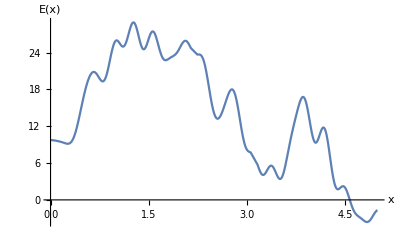

```mathematica
Plot[Realization[567,x],{x,0,5},AxesLabel->{"x","E(x)"}]
```

#### Ensemble averages and variances

```mathematica
EnsembleAverage[x_]:=Mean[Table[Realization[i,x],{i,1,R}]]
EnsembleVariance[x_]:=Variance[Table[Realization[i,x],{i,1,R}]]
```

#### Example calculation of ensemble average and variance

```mathematica
EnsembleAverage[2]
EnsembleVariance[2]
```

9.89485

94.9847

#### Plot of ensemble average and variance

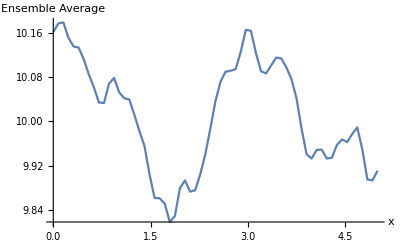

```mathematica
Plot[EnsembleAverage[x],{x,0,5},PlotPoints->2,AxesLabel->{"x","Ensemble Average"}]
```

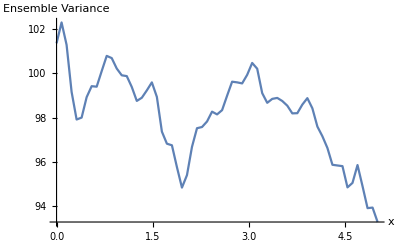

```mathematica
Plot[EnsembleVariance[x],{x,0,5},PlotPoints->2,AxesLabel->{"x","Ensemble Variance"}]
```

#### Plot of 10 realizations

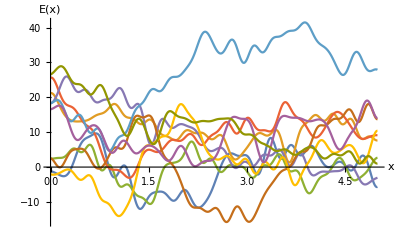

```mathematica
list={};
For[i=0,i<10,i=i+1;
AppendTo[list,Realization[i,x]]
]
Plot[list,{x,0,5},AxesLabel->{"x","E(x)"}]
```

#### Plot of 10 realizations

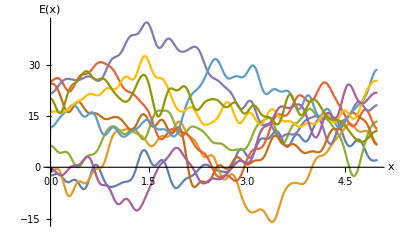

```mathematica
list={};
For[i=4300,i<4310,i=i+1;
AppendTo[list,Realization[i,x]]
]
Plot[list,{x,0,5},AxesLabel->{"x","E(x)"}]
```

#### Number of terms in the KL expansion

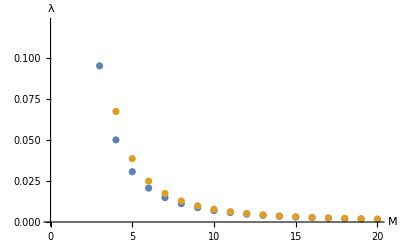

```mathematica
ListPlot[{Table[λeven[n],{n,1,M}],Table[λodd[n],{n,1,M}]},AxesLabel->{"M","λ"}] (* Justifying the number of terms in the KL expansion. *)
```

```mathematica
λeven[20]/λeven[1] (* Keep terms only with λ > λ_threshold etc. Here, λ_even_threshold = 0.0016. *)
λodd[20]/λodd[1]
```

0.00159695

0.000680913